```mathematica
Subscript[f, a_][x_,y_]:=9*x-a*x^2-3*x*y;
```

```mathematica
Subscript[g, a_][x_,y_]:=-2*y+x*y;
```

```mathematica
Subscript[F, a_][x_,y_]:={Subscript[f, a][x,y],Subscript[g, a][x,y]}
```

```mathematica
Manipulate[Show[StreamPlot[Subscript[F, a][x,y],{x,0,5},{y,0,5},StreamStyle->{Blue,Arrowheads[.03],Thick}],ListPlot[{{2,3-(2/3)a},{0,0},{9/a,0}},PlotStyle->{{Red,PointSize[0.03]}}],Frame->False,Axes->True,AxesStyle->{{Thick,Black},{Thick,Black}},AxesLabel->{"x","y"}],{a,0,8}]
```

Power::infy: Infinite expression 1/0 encountered.

```mathematica
Subscript[h, a_][x_,y_]=3-(ax)/3
```

3-ax/3

```mathematica
Subscript[j, a][x_,y_]=2
```

2

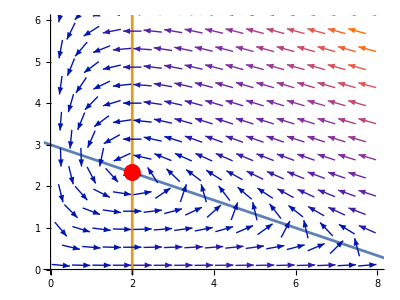

```mathematica
Show[ParametricPlot[{{u,3-(1u)/3},{2,3u}},{u,-3,9}],
ListPlot[{{2,3-(2/3)*1}},PlotStyle->{{Red,PointSize[0.03]}}],
VectorPlot[{9*x-1*x^2-3*x*y,-2*y+x*y},{x,0,8},{y,0,8}],PlotRange->{{0,8},{0,6}}]
```

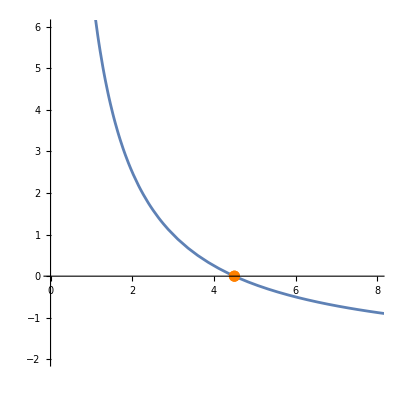

```mathematica
Show[ParametricPlot[{{u,-2+9/u}},{u,-3,9}], ListPlot[{{9/2, 0}},PlotStyle->{{Orange,PointSize[0.02]}}],PlotRange->{{0,8},{-2,6}}]
```

```mathematica
Plot[-a-sqrt(-18+4 a+a^2), {a,0,5}]
```

-Graphics-